Изобразим анимацию отображения заданной области D на верхнюю плоскость известным отображением w=f(z).

Задана область D:

```mathematica
ParametricPlot[{v Cos[u],v Sin[u]},{u,Pi,3Pi/2},{v,0,1},Frame->False,Axes->True,ImageSize ->250,AxesLabel->{Re,Im},PlotRange->{{-2,1},{-2,1}}]
```

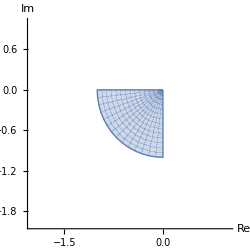

Теперь изобразим процесс перехода:

```mathematica
Animate[ With[ {z= u Exp[I v]}, Row@{ParametricPlot[ReIm[z],{v,Pi,3Pi/2},{u,0,r},AxesLabel->{Re,Im},PlotRange->{{-2,2},{-2,2}} ,Frame->False,Axes->True,ImageSize -> 300,PlotStyle->Red],ParametricPlot[ReIm[((z^2+1)/(z^2-1) )^2],{v,Pi,3Pi/2},{u,0,r},AxesLabel->{Re,Im},PlotRange->{{-6,6},{-2,6}} ,Frame->False,Axes->True,ImageSize -> 300,PlotStyle->Red]}],{r,0.001,1},AnimationRate->0.1]
```